```mathematica
thing=n(m/(2 π k T))^(1/2)Exp[-m/(2k T)v^2];
thingE = n 1/(k T)Exp[-en/(k T)];
thingEJ = 2 en^2/m^2 n 1/(k T)Exp[-en/(k T)];
```

```mathematica
thingkappa = n(1/(2 (1 - 1/(2 κ))))^(1/2)π^(-1/2)(m/(k T))^(1/2)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])(1+(m v^2)/(2κ(1-1/(2 κ))k T))^(-(κ));
```

Just the normalization

```mathematica
Integrate[thing,{v,-∞,∞},Assumptions->m>0&&k>0&&T>0]
```

n

```mathematica
midv=1/n Integrate[ v(2 thing),{v,0,∞},Assumptions->m>0&&k>0&&T>0]
```

√(2/π) √((k T)/m)

```mathematica
midv^2
```

(2 k T)/(m π)

```mathematica
Integrate[m (v-midv)^2(2 thing),{v,0,∞},Assumptions->m>0&&k>0&&T>0]
```

(k n (-2+π) T)/(2 π)

```mathematica
N[(π-2)/π]
```

0.36338

```mathematica
Integrate[m v^2 thingkappa,{v,0,∞},Assumptions->m>0&&k>0&&T>0&&κ>3/2]
```

(k n T (-1+2 κ))/(-6+4 κ)

```mathematica
Integrate[thingE,{en,0,∞},Assumptions->m>0&&k>0&&T>0]
```

n

```mathematica
Integrate[thingEJ,{en,0,∞},Assumptions->m>0&&k>0&&T>0]
```

(4 k^2 n T^2)/m^2

Now the pressure(?)

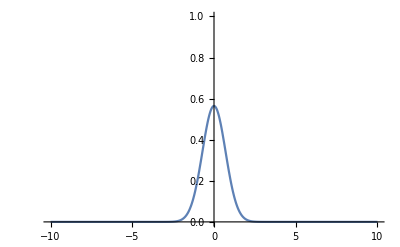

```mathematica
Plot[1/(√π)Exp[-v^2],{v,-10,10},PlotRange->{{-10,10},{0,1}}]
```

```mathematica
Integrate[1/(√π)v Exp[-v^2],{v,0,∞}]
```

1/(2 √π)